## Peocesamiento de los datos de piel normal usando mcml con fuente paralela 2 ficheros con Nr=500, Nz=400,dr=dz=0.001

Datos iniciales y abriendo el fichero

```mathematica
Nr=500;Nz=400;dr=0.001;dz=0.001;
layers={{2.5,250,0.01},{1.7,125,0.25},{1.2,125,2.5}};
zlayer={10,260,401};
SetDirectory["/home/nelia/Documents/Photodynamics/fluence/mcmlcode/paralelo/400x500"];
out=OpenRead["paralelo107.mco"];
```

1000000 Fotones

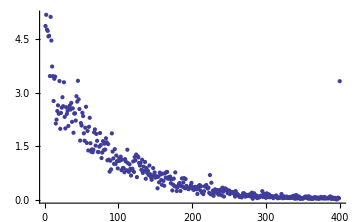
-Graphics--Graphics-

10000000 Fotones

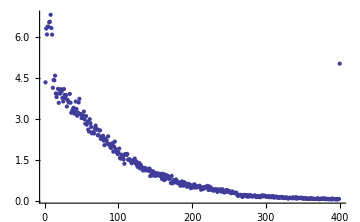
-Graphics--Graphics-

```mathematica
For[i=1,i≤10,i++,
Find[out,"A[nr-1][0]"];
Read[out,Word];
"Numero de photones";
photons=Read[out,Number];
Arz={};
ϕ={};
l=1;
"Leyendo los valores de Arz, guardandolos y normalizando" ;
"Arz/(ΔV N_fotones) ";
For[j=1,j≤ Nr,j++,
AppendTo[Arz,ReadList[out,Number,Nz]/(2 π dr^2 dz(j-0.5) photons )]
];
"Graficos de Arz";
"Calculando la fluencia ϕ=Arz/μa";
k=1;
For[j=1,j<=Nz,j++,
AppendTo[ϕ,Arz[[All,j]]/layers[[k,1]]];
If[i==zlayer[[k]],k++]
];
"Graficos de ϕ";
If[photons==1000000||photons==10000000,
Print[photons," Fotones"];
"Print[ListContourPlot[Arz,ImageSize→Medium],ListPlot[Arz[[1]],ImageSize→Medium]];";
Print[ListContourPlot[ϕ,ImageSize->Medium,PlotLabel->"Fluence"],ListPlot[ϕ[[All,10]],ImageSize->Medium]]
]
]
```

1000000 Fotones

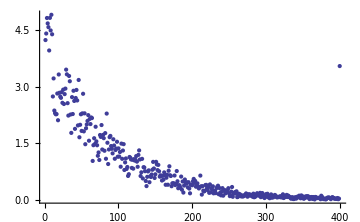
-Graphics--Graphics-

10000000 Fotones

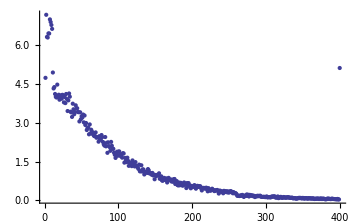
-Graphics--Graphics-

```mathematica
out=OpenRead["paralelo107.mco2"];
For[i=1,i≤10,i++,
Find[out,"A[nr-1][0]"];
Read[out,Word];
"Numero de photones";
photons=Read[out,Number];
Arz={};
ϕ={};
l=1;
"Leyendo los valores de Arz, guardandolos y normalizando" ;
"Arz/(ΔV\N_fotones) ";
For[j=1,j≤ Nr,j++,
AppendTo[Arz,ReadList[out,Number,Nz]/(2 π dr^2 dz(j-0.5) photons )]
];
"Graficos de Arz";
"Calculando la fluencia ϕ=Arz/μa";
k=1;
For[j=1,j<=Nz,j++,
AppendTo[ϕ,Arz[[All,j]]/layers[[k,1]]];
If[i==zlayer[[k]],k++]
];
"Graficos de ϕ";
If[photons==1000000||photons==10000000,
Print[photons," Fotones"];
"Print[ListContourPlot[Arz,ImageSize→Medium],ListPlot[Arz[[1]],ImageSize→Medium]];";
Print[ListContourPlot[ϕ,ImageSize->Medium,PlotLabel->"Fluence"],ListPlot[ϕ[[All,10]],ImageSize->Medium]]
]
]
```